## Wuschel-Ablated-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

This is a Cellzilla2D example that is based on the "Activator" model in 
H Jonsson, M Heisler, GV Reddy, V Agrawal, V Gor, BE Shapiro, E Mjolsness & EM Meyerowitz (2005) "Modeling the organization of the WUSCHEL expression domain in the shoot apical meristem," Bioinformatics, Vol. 21 Suppl. 1, 2005, pages i232-i240.

For more details on the model see
http://bioinformatics.oxfordjournals.org/cgi/content/abstract/21/suppl_1/i232

This CPU times shown reflect a core-i7 920 CPU

```mathematica
<<xlr8r.m;
<<Cellzilla2D.m
```

xCellerator 0.95 (28-Feb-2014) loaded Thu 15 Jun 2017 19:23:06
using Mathematica 11.1.1 for Mac OS X x86 (64-bit) (April 27, 2017) (Version 11.1, Release 1)

Cellzilla2D (3.0.51h (15 June 2017)) loaded Thu 15 Jun 2017 19:23:06
using xCellerator 0.95 and XSSA 1.3.2
GPL License Terms Apply

```mathematica
SetDirectory[NotebookDirectory[]]
FileNames["*.csv"]
```

/Users/mathman/code/cellerator/cellzilla/html/examples

{3DMeristem.csv,AMeristem.csv,Meristem.csv}

## Read the tissue and determine an approximate center

```mathematica
(* Q=CSVToTissue[ToFileName[NotebookDirectory[],"AMeristem.csv"]]; *)
ST = TemplateCircularHoneycombCover[8];
X=Centroid[ST];
XC=Mean/@Transpose[X];
```

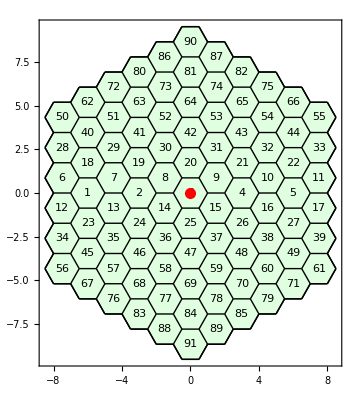

```mathematica
Show[ShowTissue[ST, Frame-> True, "CellNumbers"->True], Graphics[{Red, PointSize[.02], Point[XC]}]]
```

### Determine Central Cells to mark for ablation

```mathematica
n=NTissueCells[ST];
distancesFromCenter=1.08distance[XC,#]&/@X;
cellsInOrderOfDistanceFromCenter=Sort[Transpose[{distancesFromCenter,Range[n]}]];
```

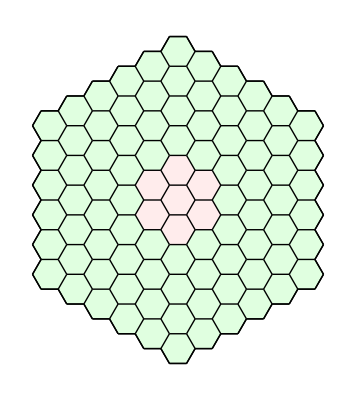

```mathematica
nablate=7;
centralCells=Last/@Table[cellsInOrderOfDistanceFromCenter[[j]],{j,1,nablate}];
ShowTissueCells[ST,centralCells]
```

## Make a tissue with the central cells ablated; need to convert to a Dynamic tissue to use DeleteCell

```mathematica
DT=Tissue2DTissue[ST];
DT=DeleteCell[DT,centralCells];
```

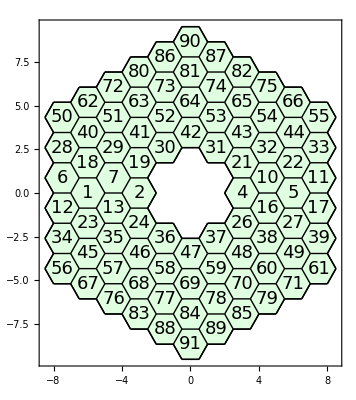

```mathematica
ShowTissue[DT, Frame-> True, "CellNumbers"-> True, "CellNumberStyle"-> 18]
```

### Convert back to static tissue to remove unneeded cells and fix cell numbers to be sequential

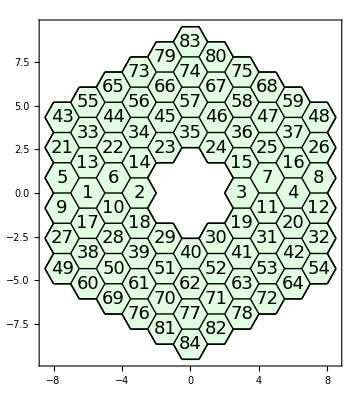

```mathematica
AST=DTissue2Tissue[DT];
ShowTissue[AST, Frame-> True, "CellNumbers"-> True, "CellNumberStyle"-> 18]
```

### DISPLAY THE CELLS ON THE BOUNDARY

```mathematica
cb=CellsOnBoundary[AST];
cb
```

{2,3,5,8,9,12,14,15,18,19,21,23,24,26,27,29,30,32,35,40,43,48,49,54,55,59,60,64,65,68,69,72,73,75,76,78,79,80,81,82,83,84}

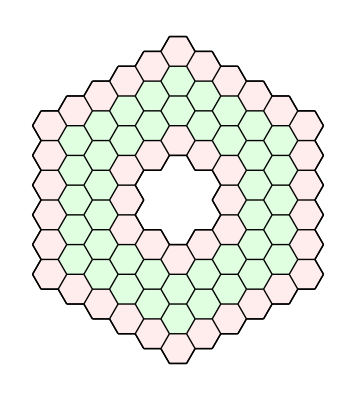

```mathematica
ShowTissueCells[AST,cb]
```

```mathematica
boundaryCentroids=1.0*Centroid[AST,cb];
distancesOfBoundaryCellsfromCenter=distance[XC,#]&/@boundaryCentroids;
boundaryDistancePairs=Transpose[{distancesOfBoundaryCellsfromCenter, cb}]
```

{{3.,2},{3.,3},{7.54983,5},{7.54983,8},{7.54983,9},{7.54983,12},{3.4641,14},{3.4641,15},{3.4641,18},{3.4641,19},{7.93725,21},{3.,23},{3.,24},{7.93725,26},{7.93725,27},{3.,29},{3.,30},{7.93725,32},{3.4641,35},{3.4641,40},{8.66025,43},{8.66025,48},{8.66025,49},{8.66025,54},{7.93725,55},{7.93725,59},{7.93725,60},{7.93725,64},{7.54983,65},{7.54983,68},{7.54983,69},{7.54983,72},{7.54983,73},{7.54983,75},{7.54983,76},{7.54983,78},{7.93725,79},{7.93725,80},{7.93725,81},{7.93725,82},{8.66025,83},{8.66025,84}}

```mathematica
innerBoundaryRadius=5;
innerBoundary=Last/@Select[boundaryDistancePairs,First[#]<innerBoundaryRadius&];
outerBoundary=Complement[cb,innerBoundary]
```

{5,8,9,12,21,26,27,32,43,48,49,54,55,59,60,64,65,68,69,72,73,75,76,78,79,80,81,82,83,84}

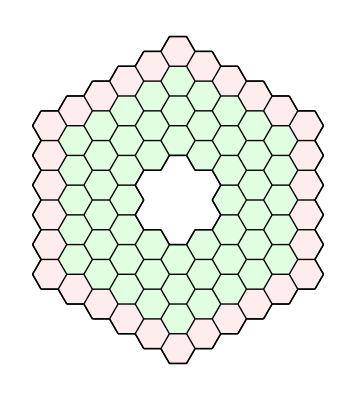

```mathematica
ShowTissueCells[AST,outerBoundary]
```

### convert to a dynamic tissue for the simulation

```mathematica
DAT=Tissue2DTissue[AST];
n=NTissueCells[DAT]
```

84

### Define the Cellerator network that will produce the ODES as specified in the model

```mathematica
net={
{Y↦W,GRN[1/tauw,Twy,1,hw,sigma]},
{A↦W,GRN[1/tauw,Twa,1,hw,sigma]},
{W->∅,dw},
(* {L1->Y+L1,ky}, *)
 
{Y->∅,dy},
{∅⇄A,a,beta},
{A+Y->Y,d},
{2 A+B->3 A,kc},
{A->B,b}
};
```

Define the initial conditions of all variables. 
Here we use zero for A,B, W, Y but that is not necessary.
L1 is an indicator function that must be 1 on the boundary and zero elsewhere.

```mathematica
rr:= RandomReal[]
```

```mathematica
ic[i_]:={A[i]->rr,B[i]->rr,W[i]->rr,Y[i]->rr};
myic=Flatten[ic/@Range[n]];
```

Define the parameters for the model

```mathematica
parameters={d-> .5,DY-> 2,  Twy->-20,Twa->0.5,(* ky->0.2, *) kz->0.2,dy->.2,dz->0.1,DZ->0.1,kD->3.0,tauw->10,dw->0.1,hw->0,a->0.1,b->0.2,beta->0.1,kc->0.1,DA->1.5,DB->15.0
};
```

Run a simulation using xlr8r

```mathematica
S=StaticSimulation[DAT,0,1000, 

 "tip"->False,
"xy"-> False, 
"CellVariable"-> area, 
"Internal"-> True, "Save"-> False, 
"Diffusion"-> {{A, DA*If[(MemberQ[{#1,#2},0] ∧  (Intersection[{#1,#2} ,outerBoundary]≠ {})),0,1]&}, {B, DB*If[(MemberQ[{#1,#2},0] ∧  (Intersection[{#1,#2} ,outerBoundary]≠ {})),0,1]&},
 {Y, DY*If[(MemberQ[{#1,#2},0] ∧  (Intersection[{#1,#2} ,outerBoundary]≠ {})),1,1]&}}, 
"Parameters"->parameters,
"Reactions"->net,
"IC"->myic,
"TestCase"->"Wuschel",
"BoundaryConditions"->{A-> 0, B-> 0, Y-> 1},
"Verbose"->True];
```

getBC: BCVars: {A,B,Y}

getBC: BCVals: {0,0,1}

getBC: missinBC: {}

getBC: BC: {A[0][t]→0,B[0][t]→0,Y[0][t]→1}

84 Cells.

9 internal reactions in each cell.

756 total intracellular reactions.

0 transport reactions.

1512 diffusion reactions.

0 algebraic equations for spring growth.

2268 total reactions.

Simulation Completed at t = 1000. after 0 cell divisions; Normal Exit. CPU: 101.721

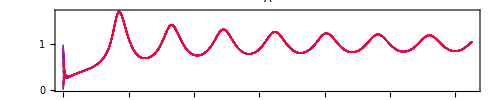
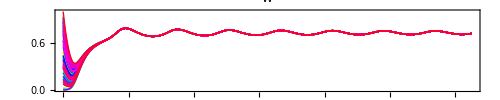
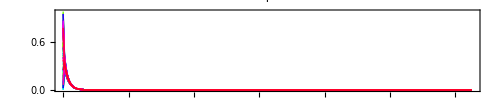

```mathematica
SimPlot[S,{A,W,Y},{0,500},PlotRange->All,AspectRatio->.2,ImageSize->500,"Points"->300]
```

Plot the results of a single variable (depending upon geometry and parameter values it can go to either a steady state or it might oscillate)

Use SimShowFinal to find the solution at the stop time of the simulation and automatically set the scales.

Warning: RGBInterpolate: xmax = 0., must be < xmin = 0.: using median value of RGBColor[Rational[1, 2], 0, Rational[1, 2]]

Warning: RGBInterpolate: xmax = 0., must be < xmin = 0.: using median value of RGBColor[Rational[1, 2], 0, Rational[1, 2]]

Warning: RGBInterpolate: xmax = 0., must be < xmin = 0.: using median value of RGBColor[Rational[1, 2], 0, Rational[1, 2]]

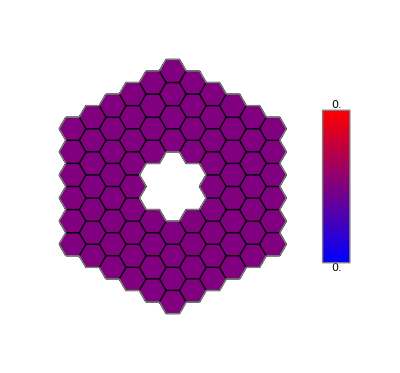

```mathematica
SimShowFinal[S,Y,AST,{Blue,Red}]
```

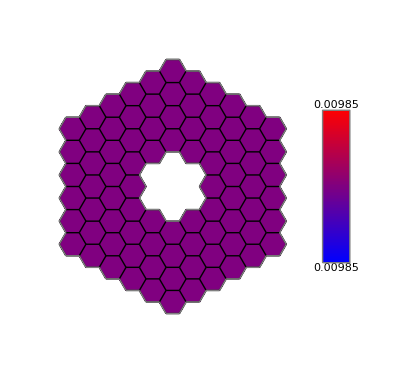

```mathematica
finalpic=SimShowAt[S,A,0.1,AST,{Blue, Red}]
```

SimAnimate will produce a sequence of plots over time. If the start and stop time are the same only one plot will be returned.

This will generate a movie of the approach towards a steady state but it can only be viewed in Mathematica

```mathematica
m=SimAnimate[S, W, q, {0,600, 120}, {LightGreen, Purple}, {0, .9}, BaseStyle-> {FontSize-> 22}, PlotLabel-> "Activator Model: WUS",
"EdgeStyles"-> Thickness[.003]];
```

```mathematica
ListAnimate[m]
```

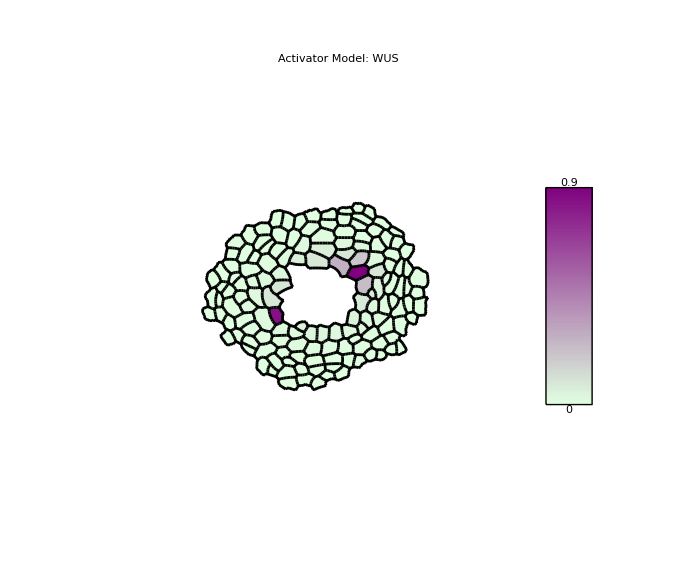

```mathematica
m//Last
```

SaveFrames, ToMOV, ToAVI create higher resolution movie files.

If ffmpeg is not installed then only the JPG files will be saved and the movie will not actually be produced. 
The built-in ffmpeg command may not work on all systems, you have to learn about ffmpeg (or avconv on 
ubuntu) to make it work from the command line if it fails.

```mathematica
m=SimAnimate[S, W, q, {0,600, 2.5}, {LightGreen, Purple}, {0, .9}, BaseStyle-> {FontSize-> 22}, PlotLabel-> "Activator Model: WUS",
"EdgeStyles"-> Thickness[.003]];
```

```mathematica
SaveFrames[m, "png", 1536, ".mov", "Ablated"]
```

Putting movie frames in  in /home/mathman/Simulations-27-Apr-13/Ablated-27-Apr-13-2029/Frames

"ffmpeg -sameq -r 16 -i 'FRAME%4d.png' '/home/mathman/Simulations-27-Apr-13/Ablated-27-Apr-13-2029/Ablated-

ffmpeg return code is: 256